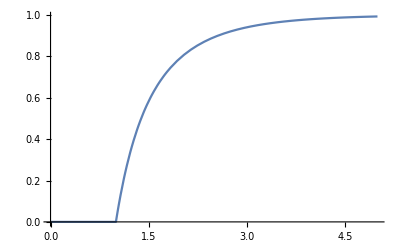

```mathematica
Plot[FindRoot[Rinf==1-Exp[-Ro*Rinf],{Rinf,1}][[1,2]],{Ro,0,5}]
```

#### Flu

```mathematica
FindRoot[Rinf==1-Exp[-1.2*Rinf],{Rinf,1}]
```

{Rinf→0.313698}

```mathematica
FindRoot[Rinf==1-Exp[-3*Rinf],{Rinf,1}]
```

{Rinf→0.94048}

```mathematica
1-1/1.2
```

0.166667

```mathematica
1-1/3.
```

0.666667

#### Rubella

```mathematica
FindRoot[Rinf==1-Exp[-6*Rinf],{Rinf,1}]
```

{Rinf→0.997484}

```mathematica
FindRoot[Rinf==1-Exp[-8*Rinf],{Rinf,1}]
```

{Rinf→0.999664}

```mathematica
1-1/6.
```

0.833333

```mathematica
1-1/8.
```

0.875

#### Measles

```mathematica
FindRoot[Rinf==1-Exp[-16*Rinf],{Rinf,1}]
```

{Rinf→1.}

```mathematica
1-1/16.
```

0.9375

```mathematica
FindRoot[Rinf==1-Exp[-18*Rinf],{Rinf,1}]
```

{Rinf→1.}

```mathematica
1-1/18.
```

0.944444

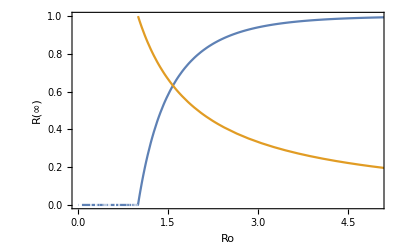

```mathematica
Plot[{FindRoot[Rinf==1-Exp[-Ro*Rinf],{Rinf,1}][[1,2]],1/Ro},{Ro,0,10},Frame->True, FrameLabel->{"Ro","R(∞)"},PlotRange->{{0,5},{0,1}}]
```